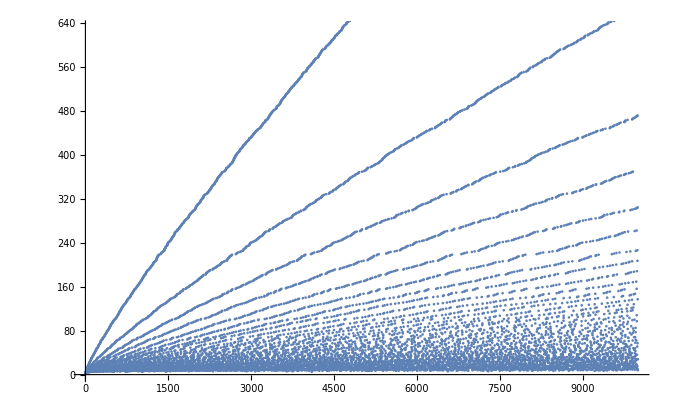

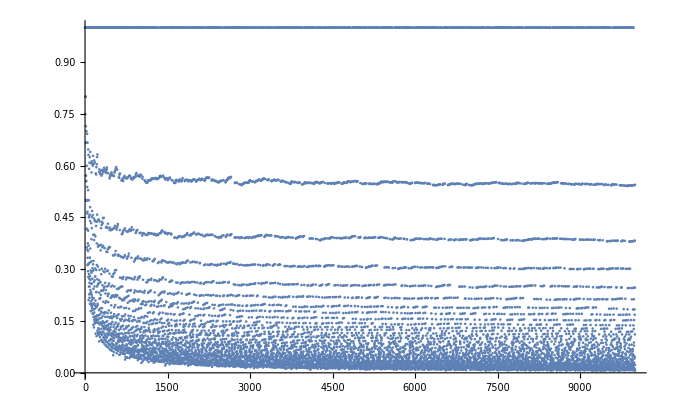

{6,12,15,18,30,42,45,48,54,60,64,90,105,140,150,162,192,210,256,320,350,375,385,405,420,450,462,486,490,512,729,960,1024,1458,1875,2304,2310,2835,2880,2916,3072,3645,3750,4096,6250,6561,7290,8750,9216,9375}

```mathematica
PrimeRead[l_]:=Module[{i,res=1},
If[l==0,Return[0]];
If[l==1,Return[1]];
For[i=1,i<=Length[l],i++,
res=res*Prime[i]^PrimeRead[l[[i]]]
];
Return[res]
]
PrimeWrite[n_]:=Module[{i,f={},res={}},
If[Or[n==0,n==1],Return[n]];
f=FactorInteger[n];
res=ConstantArray[0,PrimePi[f[[-1,1]]]];
For[i=1,i<=Length[f],i++,
res[[PrimePi[f[[i,1]]]]]=PrimeWrite[f[[i,2]]]
];
Return[res]
]
ListCost[l_]:=Module[{i},
If[¬ListQ[l],Return[1]];
Return[1+Sum[ListCost[l[[i]]],{i,1,Length[l]}]]
]
RecordBreakers[l_]:=Module[{i,rec=1,res={}},
For[i=1,i<=Length[l],i++,
If[l[[i]]<rec,AppendTo[res,i];rec=l[[i]]]
];
Return[res]
]

n=10000;

ListPlot@Table[ListCost[PrimeWrite[k]],{k,n}]
ListPlot@Table[N[ListCost[PrimeWrite[k]]/(PrimePi[k]+1)],{k,n}]
RecordBreakers[Table[N[ListCost[PrimeWrite[k]]/(PrimePi[k]+1)],{k,n}]]
Grid@Table[{k,PrimeWrite[k],ListCost[PrimeWrite[k]],N[ListCost[PrimeWrite[k]]/(PrimePi[k]+1)]},{k,n}]
```